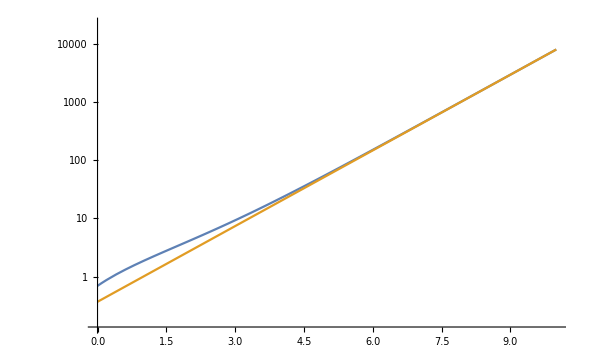

```mathematica
LogPlot[{Log[NIntegrate[Exp[b n-n Log[n]],{n,0,Infinity}]],Exp[b-1]},{b,0,10}]
```

```mathematica
s[x_]:=x^x/Exp[x]*Sqrt[2Pi x]
```

```mathematica
$Assumptions=a>0&&n>1&&b>0
```

a>0&&n>1&&b>0

```mathematica
S=Log[s[n]^a s[a]]//FullSimplify
Se=S/.a->e/n
Se//Expand
D[Se,e]//Expand//FullSimplify
Solve[%==b,e]
```

-a (1+n)+(1/2+a) Log[a]+a (1/2+n) Log[n]+1/2 (1+a) Log[2 π]

-(e (1+n))/n+(1/2+e/n) Log[e/n]+(e (1/2+n) Log[n])/n+1/2 (1+e/n) Log[2 π]

-e-e/n+1/2 Log[e/n]+(e Log[e/n])/n+e Log[n]+(e Log[n])/(2 n)+1/2 Log[2 π]+(e Log[2 π])/(2 n)

1/2 (-2+1/e+2 Log[n]+(2 Log[e]+Log[(2 π)/n])/n)

{{e→-n/(2 ProductLog[-ⅇ^(-n-b n) √(1/n) n^(1+n) √(π/2)])}}

```mathematica
e0=-n/(2 ProductLog[-ⅇ^(-n-b n) n^(1/2+n) √(π/2)])
e0//FullSimplify//Expand//FullSimplify
```

-n/(2 ProductLog[-ⅇ^(-n-b n) n^(1/2+n) √(π/2)])

-n/(2 ProductLog[-ⅇ^(-(1+b) n) n^(1/2+n) √(π/2)])

```mathematica
Solve[1/2 (-2+2 Log[n]+(2 Log[e]+Log[(2 π)/n])/n)==b,e]
```

{{e→ConditionalExpression[ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n])),-2 π<Im[2 n+2 b n-2 n Log[n]-Log[(2 π)/n]]≤2 π]}}

```mathematica
e1=ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n]))//Expand
```

ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n]))

```mathematica
Log[e1]//FullSimplify
```

n+b n-n Log[n]-1/2 Log[(2 π)/n]

```mathematica
S
```

-a (1+n)+(1/2+a) Log[a]+a (1/2+n) Log[n]+1/2 (1+a) Log[2 π]

```mathematica
Se
```

-(e (1+n))/n+(1/2+e/n) Log[e/n]+(e (1/2+n) Log[n])/n+1/2 (1+e/n) Log[2 π]

```mathematica
Se//.{e->e1}
```

-(ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n])) (1+n))/n+(1/2+ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n]))/n) Log[ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n]))/n]+(ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n])) (1/2+n) Log[n])/n+1/2 (1+ⅇ^(1/2 (2 n+2 b n-2 n Log[n]-Log[(2 π)/n]))/n) Log[2 π]

```mathematica
%//FullSimplify
```

(n^(-1/2-n) (2 ⅇ^(n+b n) (-1+b n)+n^(1/2+n) √(π/2) (2 n (1+b-Log[n])+Log[(2 π)/n])))/(2 √(2 π))

```mathematica
s[Log[n]]^(n/Log[n])s[n/Log[n]]
```

ⅇ^(-n/Log[n]) (2 π)^(1/2+n/(2 Log[n])) (n/Log[n])^(1/2+n/Log[n]) (Log[n]^(1/2+Log[n])/n)^(n/Log[n])

```mathematica
%//FullSimplify
```

ⅇ^(-n/Log[n]) √n (2 π)^((n+Log[n])/Log[n^2]) (1/Log[n])^(1/2+n/Log[n]) (Log[n]^(1/2+Log[n]))^(n/Log[n])

```mathematica
Log[%99]//FullSimplify
```

(n (-2+Log[(2 π)/Log[n]])+Log[n] (Log[(2 n π)/Log[n]]+2 n Log[Log[n]]))/(2 Log[n])

```mathematica
%103//FullSimplify//Expand
```

-n/Log[n]+(n Log[(2 π)/Log[n]])/(2 Log[n])+1/2 Log[(2 n π)/Log[n]]+n Log[Log[n]]